```mathematica
<<MathInterface`
```

```mathematica
RunAnalysis[
"/Volumes/DATA/PRL Data/EBSPEG600/20130723/m40mV2",
"qdfTrajIO",
"filter='*.qdf', nfiles=10, Rfb=9.1E+9, Cfb=1.07E-12",
"eventSegment",
"stepResponseAnalysis",
HomeDirectory[]<>"/Research/Experiments/AnalysisTools/pyEventAnalysis"
]
```

Start time: 2013-09-05 02:51 PM

[Status]
	Segment trajectory: ***NORMAL***
	Process events: ***NORMAL***


[Summary]	Baseline open channel conductance:
		Mean	= -139.36 pA
		SD	= 8.5 pA
		Slope 	= -0.09 pA/s

	Event segment stats:
		Events detected = 4378

		Open channel drift (max) = 0.05 * SD
		Open channel drift rate (min/max) = (-1.49/1.0) pA/s


[Settings]

	Trajectory I/O settings: 
		Files processed = 10
		Data path = /Volumes/DATA/PRL Data/EBSPEG600/20130723/m40mV2
		File format = qdf
		Sampling frequency = 500.0 kHz

		Feedback resistance = 9.1 GOhm
		Feedback capacitance = 1.07 pF

	Event segment settings:
		Window size for block operations = 0.5 s
		Event padding = 50 points
		Min. event rejection length = 5 points
		Event trigger threshold = 2.0 * SD

		Drift error threshold = 9999.0 * SD
		Drift rate error threshold = 100000.0 pA/s


	Event processing settings:
		Algorithm = stepResponseAnalysis

		Max. iterations  = 10000
		Fit tolerance (rel. err in leastsq)  = 1e-07
		Blockade Depth Rejection = 0.9



[Output]
	Output path = /Volumes/DATA/PRL Data/EBSPEG600/20130723/m40mV2
	Event characterization data = eventMD.tsv
	Event time-series = eventTS.csv
	Log file = eventProcessing.log

[Timing]
	Segment trajectory = 80.3 s
	Process events = 0.0 s

	Total = 80.3 s
	Time per event = 18.34 ms

```mathematica
PrintMDKeys[]
```

{blockdepth,chisq,eventend,eventstart,opencurr,status,stepheight,tau}

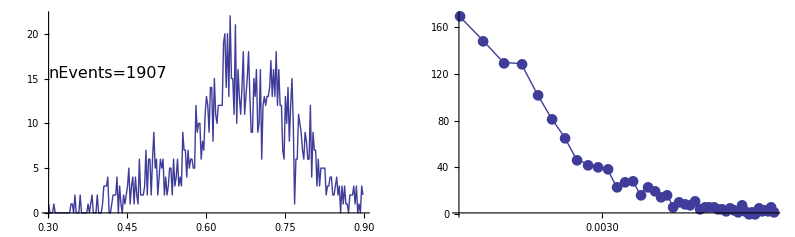

```mathematica
PlotAnalysis["/Volumes/DATA/PRL Data/EBSPEG600/20130723/m40mV2/",{0.3,0.9,0.0025},{0.001,0.01,0.0002},((#⟦MDKey["status"]⟧=="normal"&&#⟦MDKey["tau"]⟧>0.0005)&)]
```

```mathematica
PlotEvents["/Volumes/DATA/PRL Data/EBSPEG600/20130723/m40mV2",500]
```